```mathematica
RandomSeed[101];
(*Needs["PlotLegends`"]*)
LaTeX[x_]:=ToString[TeXForm[x]];
code[i_]:=Module[{},
kk=RandomChoice[{1/3,1/2,1,2,3}];
denom[x_]:=RandomChoice[{kk+x^2,x^2+x^3+kk,kk+x^3}];
wildFunction[x_]=RandomChoice[{Sin[x],E^Sin[x],E^Cos[x],E^ArcTan[x],2^Sin[x],2^Cos[x],2^ArcTan[x]}];
boundingFunction[x_]:=RandomChoice[{Sin[kk*x]^2,x^2,x^3*Sin[kk*x]}];

f[x_]=RandomChoice[{boundingFunction[x]*wildFunction[1/Surd[x,3]],boundingFunction[x]*wildFunction[1/Surd[x,3]],boundingFunction[x]/denom[x],boundingFunction[x]*wildFunction[1/Surd[x,3]],boundingFunction[x]*Erf[kk*x]}];
switch=Random[Integer,{1,6}];
fxns[1]={f[x],f'[x],f''[x]};
fxns[2]={f[x],f''[x],f'[x]};
fxns[3]={f'[x],f[x],f''[x]};
fxns[4]={f''[x],f[x],f'[x]};
fxns[5]={f'[x],f''[x],f[x]};
fxns[6]={f''[x],f'[x],f[x]};
graphfxns=fxns[switch];
verify[1]=If[switch==1,"[correct]",""];
verify[2]=If[switch==2,"[correct]",""];
verify[3]=If[switch==3,"[correct]",""];
verify[4]=If[switch==4,"[correct]",""];
verify[5]=If[switch==5,"[correct]",""];
verify[6]=If[switch==6,"[correct]",""];
graph=Plot[graphfxns,{x,-5,5},Ticks->False,PlotStyle->{{Thick,Black} ,{Thick,Black,Dashed},{Thick,Black,Dotted}},PlotLegends->{TraditionalForm[f],TraditionalForm[g],TraditionalForm[h]}];
{graph,
StringJoin["\\documentclass{ximera}
\\input{../preamble.tex}
\\author{Bart Snapp}
\\license{Creative Commons 3.0 By-NC}
\\begin{document}
\\begin{exercise}
\\outcome{Identify the relationships between the function and its first and second derivatives.}
\\tag{derivative}
Here we see a plot of $f$, $g$, and $h$. 
\\begin{image}
\\includegraphics[width=.5\\textwidth]{graphFGH",LaTeX[i],".png}
\\end{image}
Which of the following is correct?
\\begin{multipleChoice}
\\choice",verify[1],"{$f'(x) = g(x)$ and $f''(x) = h(x)$}
\\choice",verify[2],"{$f'(x) = h(x)$ and $f''(x) = g(x)$}
\\choice",verify[3],"{$g'(x) = f(x)$ and $g''(x) = h(x)$}
\\choice",verify[4],"{$g'(x) = h(x)$ and $g''(x) = f(x)$}
\\choice",verify[5],"{$h'(x) = f(x)$ and $h''(x) = g(x)$}
\\choice",verify[6],"{$h'(x) = g(x)$ and $h''(x) = f(x)$} 
\\end{multipleChoice}
\\end{exercise}
\\end{document}"]}]
```

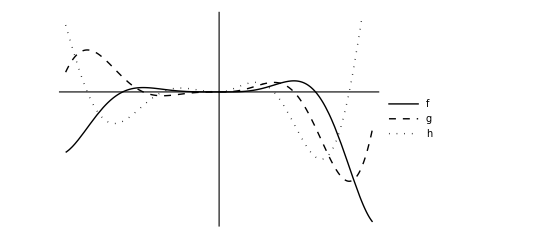
{-Graphics-,\documentclass{ximera}
\input{../preamble.tex}
\author{Bart Snapp}
\license{Creative Commons 3.0 By-NC}
\begin{document}
\begin{exercise}
\outcome{Identify the relationships between the function and its first and second derivatives.}
\tag{derivative}
Here we see a plot of $f$, $g$, and $h$. 
\begin{image}
\includegraphics[width=.5\textwidth]{graphFGH6.png}
\end{image}
Which of the following is correct?
\begin{multipleChoice}
\choice[correct]{$f'(x) = g(x)$ and $f''(x) = h(x)$}
\choice{$f'(x) = h(x)$ and $f''(x) = g(x)$}
\choice{$g'(x) = f(x)$ and $g''(x) = h(x)$}
\choice{$g'(x) = h(x)$ and $g''(x) = f(x)$}
\choice{$h'(x) = f(x)$ and $h''(x) = g(x)$}
\choice{$h'(x) = g(x)$ and $h''(x) = f(x)$} 
\end{multipleChoice}
\end{exercise}
\end{document}}

```mathematica
code[6]
```

```mathematica
Do[{precode=code[i];	
Export["identifyFirstSecondDeriv"<>ToString[i]<>".tex",precode[[2]],"Text"];
Export["graphFGH"<>ToString[i]<>".png",precode[[1]],"PNG",ImageResolution->200]}
,{i,12}];
```